# Learning Neural Networks Part I

## Introduction

Let’s start with the simplest possible example: a single neuron.

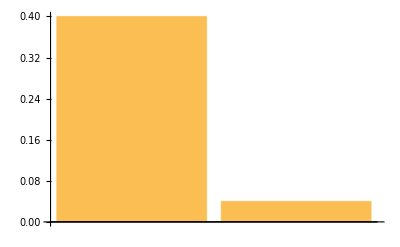

```mathematica
activationFunction = Tanh[x];
weight = .1;
bias = .1;
input = .4;
BarChart[{input, activationFunction /. {x-> weight * input}}]
```